```mathematica
ClearAll["Global`*"]

v[s_] = c1+c2*s+c3*Cos[α*s]+c4*Sin[α*s];

{RR, MM} = CoefficientArrays[
{
v[0]==0,
-v''[0] == -β/l*v'[0],
-v''[l]==0,
-(v'''[l]+α^2*v'[l])==0
},
{c1,c2,c3,c4}
]//Normal;
RR = -RR;
MatrixForm[MM]
MatrixForm[RR]
```

(1 | 0 | 1 | 0
0 | β/l | α^2 | (α β)/l
0 | 0 | α^2 Cos[l α] | α^2 Sin[l α]
0 | -α^2 | 0 | 0)

(0
0
0
0)

```mathematica
detMM[α_,β_] = Det[MM]//Simplify
```

α^5 ((β Cos[l α])/l-α Sin[l α])

```mathematica
Manipulate[
Plot[detMM[α, β]/.l->1, {α, 0, 5}, AxesLabel->{"α", "det(M)"}],
{β, {1,5,10,20}}]
```

## β = 1

```mathematica
l=1;
αcr = α/.FindRoot[detMM[α, 1]==0, {α,3}]
αcr^2
ξ = αcr^2/Pi^2
l0 = l/Sqrt[ξ]
```

3.42562

11.7349

1.18899

0.917088

```mathematica
Mcr = MM/.α->αcr/.β->1//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 1 | 11.7349 | 3.42562
0 | 0 | -11.2647 | -3.28837
0 | -11.7349 | 0 | 0)

```mathematica
Eigensystem[Mcr]
```

{{-5.13235+1.61041 ⅈ,-5.13235-1.61041 ⅈ,1.,3.62974×10^-14},{{-0.0671094+8.89081×10^-17 ⅈ,-0.358805+0.112584 ⅈ,0.411538-0.108073 ⅈ,-0.820388+0. ⅈ},{-0.0671094-8.89081×10^-17 ⅈ,-0.358805-0.112584 ⅈ,0.411538+0.108073 ⅈ,-0.820388+0. ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.269829+0. ⅈ,2.60444×10^-15+0. ⅈ,0.269829+0. ⅈ,-0.92433+0. ⅈ}}}

```mathematica
{c1,c2,c3,c4} =Eigenvectors[Mcr]//Re//Chop//Last
```

{-0.269829,0,0.269829,-0.92433}

```mathematica
v[s]
v[s]/c4//Simplify
```

-0.269829+0.269829 Cos[s α]-0.92433 Sin[s α]

0.291918-0.291918 Cos[s α]+1. Sin[s α]

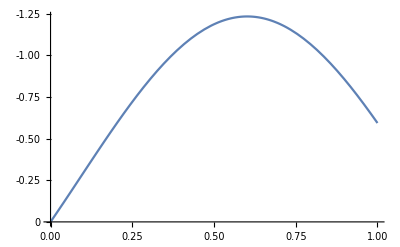

```mathematica
Plot[v[s]/.α->.9αcr, {s, 0, l}, ScalingFunctions->"Reverse"]
```

## β = 5

```mathematica
l=1;
αcr = α/.FindRoot[detMM[α, 5]==0, {α,2}]
αcr^2
ξ = αcr^2/Pi^2
l0 = l/Sqrt[ξ]
```

1.31384

1.72617

0.174898

2.39116

```mathematica
Mcr = MM/.α->αcr/.β->5//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 5 | 1.72617 | 6.56919
0 | 0 | 0.438689 | 1.66949
0 | -1.72617 | 0 | 0)

```mathematica
Eigensystem[Mcr]
```

{{2.71934+2.47753 ⅈ,2.71934-2.47753 ⅈ,1.,-6.22865×10^-17},{{0.0558107+0.0391583 ⅈ,0.883798+0. ⅈ,-0.00105797+0.205599 ⅈ,-0.306554+0.279294 ⅈ},{0.0558107-0.0391583 ⅈ,0.883798+0. ⅈ,-0.00105797-0.205599 ⅈ,-0.306554-0.279294 ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.695208+0. ⅈ,2.10214×10^-17+0. ⅈ,0.695208+0. ⅈ,-0.182678+0. ⅈ}}}

```mathematica
{c1,c2,c3,c4} =Eigenvectors[Mcr]//Re//Chop//Last
```

{-0.695208,0,0.695208,-0.182678}

```mathematica
v[s]
v[s]/c1//Simplify
```

-0.695208+0.695208 Cos[s α]-0.182678 Sin[s α]

1.-1. Cos[s α]+0.262768 Sin[s α]

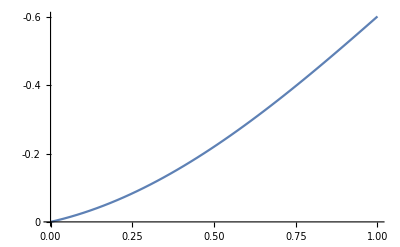

```mathematica
Plot[v[s]/.α->.9αcr, {s, 0, l}, ScalingFunctions->"Reverse"]
```

## β = 10

```mathematica
l=1;
αcr = α/.FindRoot[detMM[α, 10]==0, {α,2}]
αcr^2
ξ = αcr^2/Pi^2
l0 = l/Sqrt[ξ]
```

1.42887

2.04167

0.206864

2.19866

```mathematica
Mcr = MM/.α->αcr/.β->10//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 10 | 2.04167 | 14.2887
0 | 0 | 0.288795 | 2.02114
0 | -2.04167 | 0 | 0)

```mathematica
Eigensystem[Mcr]
```

{{5.1444+2.36557 ⅈ,5.1444-2.36557 ⅈ,1.,-2.66942×10^-16},{{-0.0044052+0.0260076 ⅈ,0.932902+0. ⅈ,-0.0797797+0.0973648 ⅈ,-0.30562+0.140535 ⅈ},{-0.0044052-0.0260076 ⅈ,0.932902+0. ⅈ,-0.0797797-0.0973648 ⅈ,-0.30562-0.140535 ⅈ},{1.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ},{-0.703525+0. ⅈ,-2.21088×10^-16+0. ⅈ,0.703525+0. ⅈ,-0.100525+0. ⅈ}}}

```mathematica
{c1,c2,c3,c4} =Eigenvectors[Mcr]//Re//Chop//Last
```

{-0.703525,0,0.703525,-0.100525}

```mathematica
v[s]
v[s]/c1//Simplify
```

-0.703525+0.703525 Cos[s α]-0.100525 Sin[s α]

1.-1. Cos[s α]+0.142887 Sin[s α]

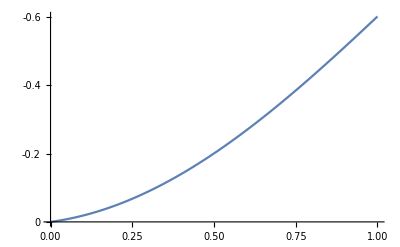

```mathematica
Plot[v[s]/.α->.9αcr, {s, 0, l}, ScalingFunctions->"Reverse"]
```

## β = 20

```mathematica
l=1;
αcr = α/.FindRoot[detMM[α, 20]==0, {α,1.5}]
αcr^2
ξ = αcr^2/Pi^2
l0 = l/Sqrt[ξ]
```

1.49613

```mathematica
Mcr = MM/.α->αcr/.β->20//Chop;
MatrixForm[Mcr]
```

(1 | 0 | 1 | 0
0 | 20 | 2.2384 | 29.9226
0 | 0 | 0.16698 | 2.23216
0 | -2.2384 | 0 | 0)

```mathematica
Eigensystem[Mcr]
```

{{15.6833,4.48363,1.,-1.98973×10^-16},{{-0.00138402,0.989762,-0.020322,-0.141264},{0.0644676,-0.869935,0.224582,0.434305},{1.,0.,0.,0.},{-0.70612,1.15967×10^-16,0.70612,-0.0528223}}}

```mathematica
{c1,c2,c3,c4} =Eigenvectors[Mcr]//Re//Chop//Last
```

{-0.70612,0,0.70612,-0.0528223}

```mathematica
v[s]
v[s]/c1//Simplify
```

-0.70612+0.70612 Cos[s α]-0.0528223 Sin[s α]

1.-1. Cos[s α]+0.0748064 Sin[s α]

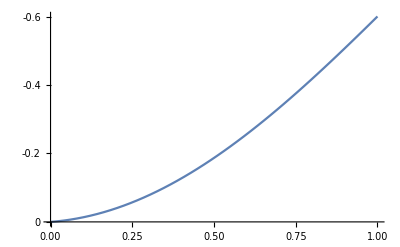

```mathematica
Plot[v[s]/.α->.9αcr, {s, 0, l}, ScalingFunctions->"Reverse"]
```